```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../plots/plots-109";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
statsDir = "../../runs/Stats-109";
```

```mathematica
alpha = Import["../../runs/Stats-106/alpha.dat"];
```

```mathematica
$N = 4;$K=9;
data = Import[statsDir<>"/N4K9/5-Re.dat"];
```

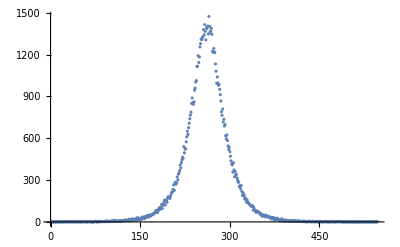

```mathematica
ListPlot[data[[2]], PlotRange->All]
```

```mathematica
randmats = Partition[(# - 1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1/(√($N)), $N], {100000*$K}], $K];
```

```mathematica
n = 5;
d = Tr[Dot@@Table[#[[n]], {A, 1, n}]]&/@randmats;
```

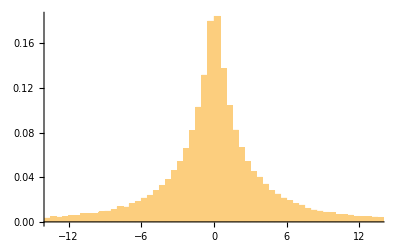

```mathematica
Histogram[{Standardize[Re[d]], }, 450, PDF]
```